```mathematica
G=Table[RotationMatrix[(j-1)*π/3].{0,√3},{j,1,6}];
{G1,G2,G3,G4,G5,G6}=G;
shell[n_]:=Block[{p,l,i},
p=n*G1;
l={p};
For[i=1,i≤n,i=i+1,p=p+G3; AppendTo[l,p]];
For[i=1,i≤n,i=i+1,p=p+G4; AppendTo[l,p]];
For[i=1,i≤n,i=i+1,p=p+G5; AppendTo[l,p]];
For[i=1,i≤n,i=i+1,p=p+G6; AppendTo[l,p]];
For[i=1,i≤n,i=i+1,p=p+G1; AppendTo[l,p]];
For[i=1,i≤n-1,i=i+1,p=p+G2; AppendTo[l,p]];
l
]
FF[n_,m_]:=Block[{l},
l=None;
If[n==1&&m==1,l=1];
If[n≥2&&m≥1&&m≤6*(n-1),l=3*(n-1)*(n-2)+m+1];
l
]
(*The link number up to shell 10*)
(*Link10=Import["C:\\Users\\wufch\\Dropbox\\graphene_superconductivity\\anomalous Hall state\\band_structure\\Link10.dat","Data"]*)Link10=Import[NotebookDirectory[]<>"Link10.dat","Data"];

Link[n_]:=Block[{l},
l=Drop[Link10,{6*FF[n,6*(n-1)]+1,Length[Link10]}];
l=Select[l,#⟦2⟧<=FF[n,6*(n-1)]&];
l]
Shell[n_]:=Flatten[Table[shell[i-1],{i,1,n}],1]; 
check[n_]:=Block[{L,S},
L=Link[n];
S=Shell[n];
Table[Norm[S⟦L⟦i,1⟧⟧-S⟦L⟦i,2⟧⟧-G⟦L⟦i,3⟧⟧],{i,1,Length[L]}]
]
```

```mathematica
ℏ=1.054571800*10^-34; (*J.s*)
me=9.10938356*10^-31;(* kilograms*);
e=1.60217662*10^-19(* coulombs *);
mb=0.65*me(*effective mass for MoTe2*);
mt=0.35*me(*effective mass for WSe2*);
```

```mathematica
(*aM is in unit of nm, energy is in unit of meV, ψb & ψt are in unit of radian*)
```

```mathematica
HH[n_,aM_,kx_,ky_,Vb_,ψb_,Vt_,ψt_,w_,Vt0_]:=Block[{NN,hh,L,S,κbx,κby,κtx,κty,q1,αb,αt,Bb,Bt,T12,T21,i,l,Qx,Qy,ω},
{κbx,κby}={-1/2,(√3)/2};
{κtx,κty}={1/2,(√3)/2};
q1=(4π)/(3*(aM*10^-9))(*m^-1*); 
αb=(ℏ^2*q1^2)/(2*mb)/e*1000(*meV*);
αt=(ℏ^2*q1^2)/(2*mt)/e*1000(*meV*);


NN=FF[n,6*(n-1)];
hh=0*IdentityMatrix[2*NN];
L=Link[n];
S=Shell[n];

Bb=Vb*{Exp[ⅈ ψb],Exp[-ⅈ ψb],Exp[ⅈ ψb],Exp[-ⅈ ψb],Exp[ⅈ ψb],Exp[-ⅈ ψb]};
Bt=Vt*{Exp[ⅈ ψt],Exp[-ⅈ ψt],Exp[ⅈ ψt],Exp[-ⅈ ψt],Exp[ⅈ ψt],Exp[-ⅈ ψt]};


For[i=1,i≤Length[S],i=i+1,
Qx=kx+S⟦i,1⟧;
Qy=ky+S⟦i,2⟧;
hh⟦2*i-1,2*i-1⟧= -αb*((Qx-κbx)^2+(Qy-κby)^2);
hh⟦2*i,2*i⟧= -αt*((Qx-κtx)^2+(Qy-κty)^2)+Vt0;
];

For[l=1,l≤Length[L],l=l+1,
hh⟦2* L⟦l,1⟧-1,2*L⟦l,2⟧-1⟧=Bb⟦L⟦l,3⟧⟧;
hh⟦2* L⟦l,1⟧,2*L⟦l,2⟧⟧=Bt⟦L⟦l,3⟧⟧;
];


ω=Exp[ⅈ (2π)/3];

T12=w*{0,ω,ω^2,0,0,0};
T21=w*{0,0,0,0,Conjugate[ω],(Conjugate[ω])^2};

For[i=1,i≤Length[S],i=i+1,
hh⟦2*i-1,2*i⟧= w;
hh⟦2*i,2*i-1⟧=w;
];


For[l=1,l≤Length[L],l=l+1,
hh⟦2* L⟦l,1⟧-1,2*L⟦l,2⟧⟧=T12⟦L⟦l,3⟧⟧;
hh⟦2* L⟦l,1⟧,2*L⟦l,2⟧-1⟧=T21⟦L⟦l,3⟧⟧;
];

hh

]
```

```mathematica
κb={-1/2,(√3)/2};
κt={1/2,(√3)/2};
KPath={κt,κb,{0,0}};
hPath={0,1,1+1};
NN=50;
KKPath=Flatten[Table[KPath⟦j⟧+(KPath⟦j+1⟧-KPath⟦j⟧)*i/NN,{j,1,Length[KPath]-1},{i,0,NN}],1];
hhPath=Flatten[Table[hPath⟦j⟧+(hPath⟦j+1⟧-hPath⟦j⟧)*i/NN,{j,1,Length[hPath]-1},{i,0,NN}],1];
```

```mathematica
En[n_,aM_,Vb_,ψb_,Vt_,ψt_,w_,Vt0_]:=ParallelTable[Sort[Eigenvalues[HH[n,aM,N[KKPath⟦i,1⟧],N[KKPath⟦i,2⟧],Vb,ψb,Vt,ψt,w,Vt0]],#1>#2&],{i,1,Length[KKPath]}];
```

```mathematica
band[n_,aM_,Vb_,ψb_,Vt_,ψt_,w_,Vt0_]:=Block[{en,En0},

en=En[n,aM,Vb,ψb,Vt,ψt,w,Vt0];
Table[{hhPath⟦i⟧,en⟦i,j⟧},{j,1,Length[en⟦1⟧]},{i,1,Length[en]}]]
```

```mathematica
plot[n_,aM_,Vb_,ψb_,Vt_,ψt_,w_,Vt0_,min_,max_]:=ListLinePlot[band[n,aM,Vb,ψb,Vt,ψt,w,Vt0],GridLines->{Join[hPath,{1/2}],None},Frame->True,PlotRange->{{hPath⟦1⟧,hPath⟦-1⟧},{min,max}},PlotStyle->ColorData[97,"ColorList"]⟦-4⟧,FrameTicks->{{True,None},{{{0,"κ_t"},{1/2,"m"},{1,"κ_b"},{1+1,"γ"}},None}},GridLinesStyle->Directive[Black],FrameStyle->Black,FrameTicksStyle->Directive[{Thick,Black,18}],AspectRatio->GoldenRatio]
```

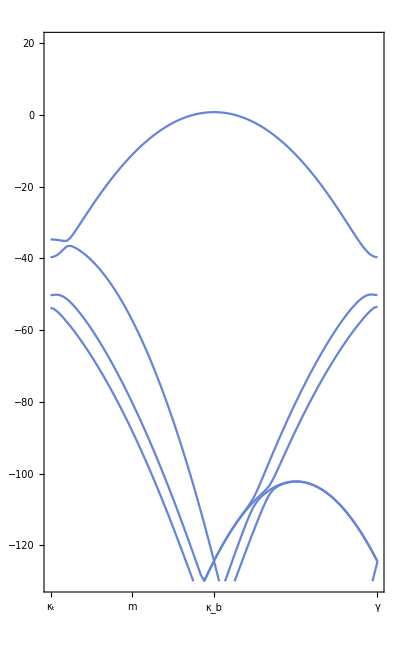

```mathematica
plot[6,4.62,4.1,14/180*π,0,0,1.3,-35,-130,20]
```

```mathematica
enκtgap[n_,aM_,Vb_,ψb_,Vt_,ψt_,w_,Vt0_]:=Block[{en,gap},
en=Sort[Eigenvalues[HH[n,aM,N[κt⟦1⟧],N[κt⟦2⟧],Vb,ψb,Vt,ψt,w,Vt0]],#1>#2&];
gap=en⟦1⟧-en⟦2⟧;
gap
]
```

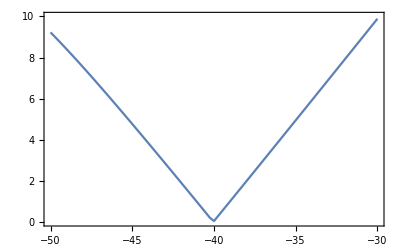

```mathematica
ListLinePlot[Table[{Vt0,enκtgap[6,4.62,4.1,14/180*π,0,0,1.3,Vt0]},{Vt0,-50,-30,0.25}],PlotRange->{{-50,-30},{0,10}},Frame->True,AspectRatio->1/GoldenRatio]
```

```mathematica
eigsys[n_,aM_,kx_,ky_,Vb_,ψb_,Vt_,ψt_,w_,Vt0_]:=Block[{hh,eigen,eig,NN,evalue,evector},
hh=HH[n,aM,kx,ky,Vb,ψb,Vt,ψt,w,Vt0];
eigen=Eigensystem[hh];
eig=Table[{eigen⟦1,i⟧,Normalize[eigen⟦2,i⟧]},{i,1,Length[eigen⟦1⟧]}];
eig=Sort[eig,#1⟦1⟧>#2⟦1⟧&];
{eig⟦1⟧,eig⟦2⟧}
]
```

```mathematica
.
```

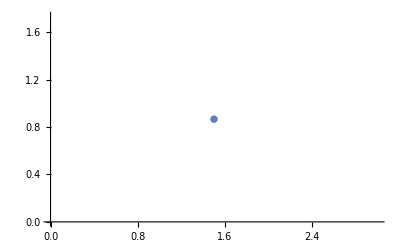

```mathematica
ListPlot[{G6}]
```

```mathematica
Nk = 36;
b1 =G6;
b2 =G2 ;
kk=Table[b1 * i / Nk +b2 * j/ Nk,{i,0, Nk}, {j, 0, Nk }];
```

```mathematica
Bcurvature[list_]:=1/(3√3/(2*Nk*Nk))ParallelTable[Arg[(Conjugate[list⟦i,j⟧].list⟦i+1,j⟧)*(Conjugate[list⟦i+1,j⟧].list⟦i+1,j+1⟧)*(Conjugate[list⟦i+1,j+1⟧].list⟦i,j+1⟧)*(Conjugate[list⟦i,j+1⟧].list⟦i,j⟧)],{i,1,Nk},{j,1,Nk}];
chern[list_]:=1/(2π)Total[list]/Length[list]*(3*(√3)/2);
```

```mathematica
berryC[n_,aM_,Vb_,ψb_,Vt_,ψt_,w_,Vt0_]:=Block[{EnVec,BC1,BC2},
EnVec=ParallelTable[eigsys[n,aM,N[kk⟦i,j,1⟧],N[kk⟦i,j,2⟧],Vb,ψb,Vt,ψt,w,Vt0],{i,1,Nk+1},{j,1,Nk+1}];
BC1=Bcurvature[Table[EnVec⟦i,j,1,2⟧,{i,1,Nk+1},{j,1,Nk+1}]];
BC2=Bcurvature[Table[EnVec⟦i,j,2,2⟧,{i,1,Nk+1},{j,1,Nk+1}]];
{chern[Flatten[BC1,1]],chern[Flatten[BC2,1]],ListDensityPlot[Flatten[Table[{kk⟦i,j,1⟧,kk⟦i,j,2⟧,BC1⟦i,j⟧},{i,1,Nk},{j,1,Nk}],1],AspectRatio->Automatic,PlotLegends->All,Frame->None,ColorFunction->"LightTemperatureMap",PlotRange->All],ListDensityPlot[Flatten[Table[{kk⟦i,j,1⟧,kk⟦i,j,2⟧,BC2⟦i,j⟧},{i,1,Nk},{j,1,Nk}],1],AspectRatio->Automatic,PlotLegends->All,Frame->None,ColorFunction->"LightTemperatureMap",PlotRange->All]}
];
```

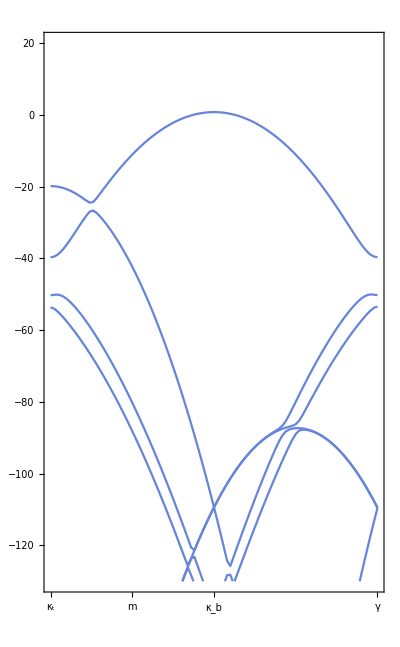

```mathematica
plot[6,4.62,4.1,14/180*π,0,0,1.3,-20,-130,20]
```

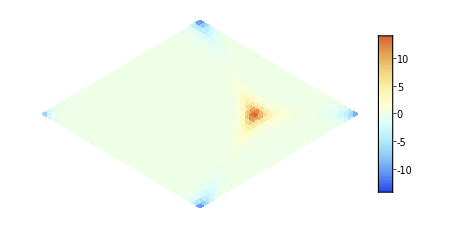
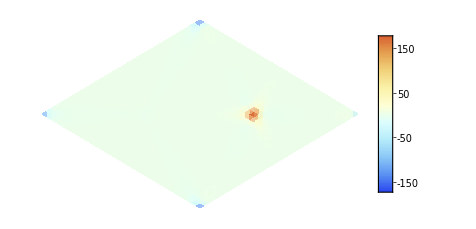
{-6.80109×10^-17,1.61413×10^-14,-Graphics-,-Graphics-}

```mathematica
berryC[6,4.62,4.1,14/180*π,0,0,1.3,-100]
```

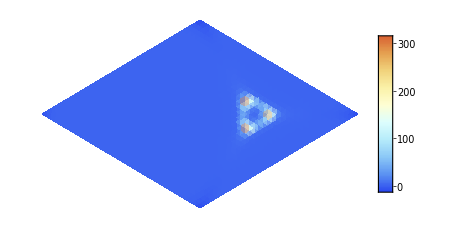
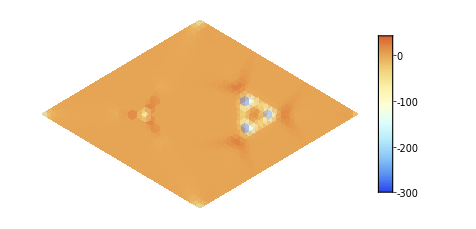
{1.,-1.,-Graphics-,-Graphics-}

```mathematica
berryC[6,4.62,4.1,14/180*π,0,0,1.3,-35]
```

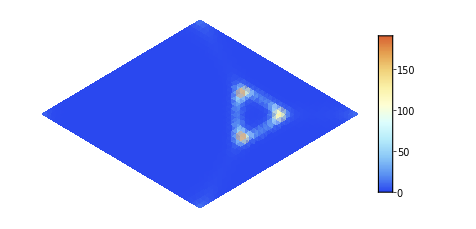
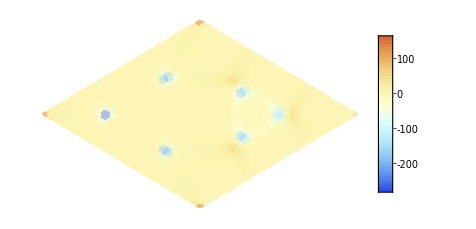
{1.,-1.,-Graphics-,-Graphics-}

```mathematica
berryC[6,4.62,4.1,-14/180*π,4.1,240/180*π,1.3,-30]
```

```mathematica
berryC[6,4.62,4.1,-14/180*π,4.1,240/180*π,1.3,0]
```

{1.,-1.,-Graphics-,-Graphics-}

```mathematica
berryC[6,4.62,4.1,-14/180*π,4.1,240/180*π,1.3,-30]
```

{1.,-1.,-Graphics-,-Graphics-}

```mathematica
berryC[6,4.65,10.1,-14/180*π,10.1,240/180*π,1.3,0]
```

{1.,-1.,-Graphics-,-Graphics-}

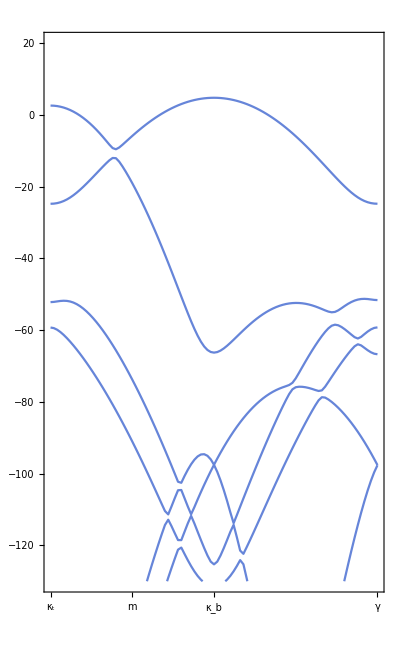

```mathematica
plot[6,4.65,10.1,-14/180*π,10.1,240/180*π,1.3,0,-130,20]
```

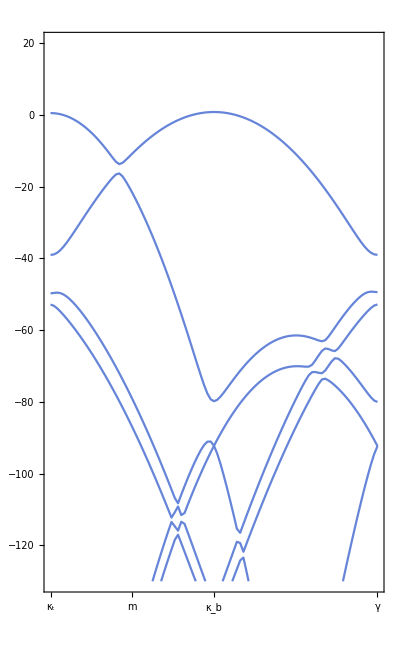

```mathematica
plot[6,4.65,4.1,-14/180*π,4.1,240/180*π,1.3,-0,-130,20]
```

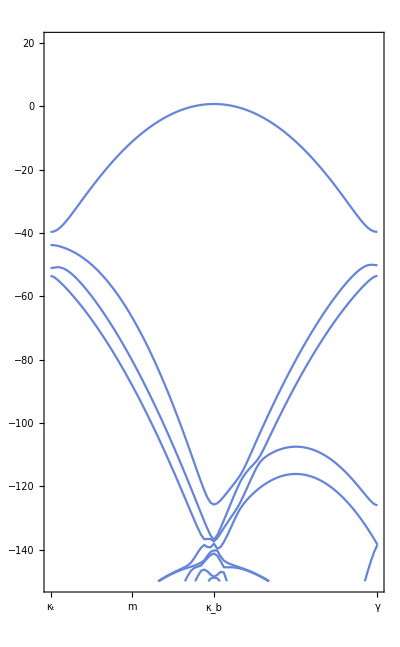

```mathematica
plot[6,4.62,4.1,-14/180*π,4.1,240/180*π,1.3,-45,-150,20]
```